```mathematica
Notebook for the polynomial method in the Dirac-Weyl equation. 
This example is for the case of the zigzag-like hexagonal graphene flake, but it can be modified to suit other systems/boundary conditions.
```

```mathematica
Silencing the "evaluation is zero" warning messages;
```

```mathematica
ParallelEvaluate[Off[NIntegrate::ncvb];
Off[NIntegrate::slwcon];
Off[NIntegrate::eincr];
Off[NIntegrate::oidiv];
Off[NIntegrate::izero];];
```

```mathematica
Defining physical constants and stuff;
```

```mathematica
ℏ=1.;
vf=1.;
L=1.;
sqrt3=N[√3];
size=15.;
```

```mathematica
Creating data folder;
```

```mathematica
shape="hexagon";
folder="~/agr_tese/data/schrodinger/"<>shape<>"_";
basissize=ToString[Floor[size]];
CreateDirectory[folder<>basissize]//Quiet;
```

```mathematica
Defining the billiard region;
The region plot is just to double check if the boundaries are well-defined;
```

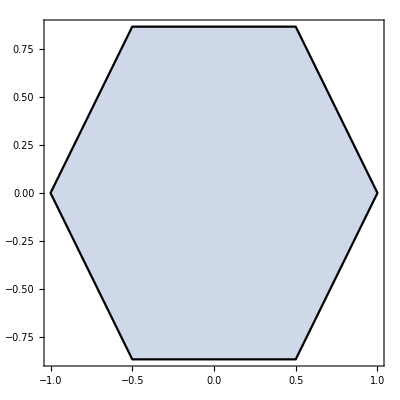

```mathematica
RegionPlot[-L+RealAbs[y]/sqrt3≤x≤L-RealAbs[y]/sqrt3&&-sqrt3/2*L≤y≤sqrt3/2*L,{x,-L,L} ,{y,-L,L}];
reg=Polygon[CirclePoints[L,6]];
RegionPlot[reg,Axes->True,AxesStyle->Directive[Black,Thickness[0.001]],BoundaryStyle->Black,ImageSize->Full]
```

```mathematica
Defining the scalar product, the norm, and the Hamiltonian matrix element;
```

```mathematica
MyNorm[func1_]:=√NIntegrate[(func1[x,y])^2,{y,-sqrt3/2*L,sqrt3/2*L},{x,-L+RealAbs[y]/sqrt3,L-RealAbs[y]/sqrt3},Method->{"LocalAdaptive",Method->"LobattoKronrodRule","SymbolicProcessing"->0.0001}]
MyProd[func1_,func2_]:=NIntegrate[func1[x,y]*func2[x,y],{y,-sqrt3/2*L,sqrt3/2*L},{x,-L+RealAbs[y]/sqrt3,L-RealAbs[y]/sqrt3},Method->{"LocalAdaptive",Method->"LobattoKronrodRule","SymbolicProcessing"->0.0001}]
En[f1_,f2_]:=-Chop[NIntegrate[Chop[Simplify[(f1[x,y])*(D[f2[x,y],{x,2}]+D[f2[x,y],{y,2}])]],{y,-sqrt3/2*L,sqrt3/2*L},{x,-L+RealAbs[y]/sqrt3,L-RealAbs[y]/sqrt3},Method->{"LocalAdaptive",Method->"LobattoKronrodRule","SymbolicProcessing"->0.01},AccuracyGoal->10,PrecisionGoal->10]]
```

```mathematica
NUMERICAL EIGENVALUES;
```

```mathematica
exact=(4Tan[π/6])/6*NDEigenvalues[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈reg,Floor[size]]
```

```mathematica
Define the initial functions here;
```

```mathematica
ϕu[1,x_,y_]=(y-sqrt3/2 L)*(y+sqrt3/2 L)*(x-sqrt3/3 y-L)*(x-sqrt3/3 y+L)*(x+sqrt3/3 y-L)*(x+sqrt3/3 y+L);
ϕn[1,x_,y_]=Simplify[(1/(MyNorm[ϕu[1,#1,#2]&]))ϕu[1,x,y]];
En[ϕn[1,#1,#2]&,ϕn[1,#1,#2]&]
```

7.26185

```mathematica
Gram-Schmidt Process for 2-band models;
This defines the Basis object;
```

```mathematica
f[m_,x_,y_]:=If[Mod[(m-1)-(Floor[√(m-1)])^2,2]==0,x^Floor[√(m-1)]*y^(((m-1)-(Floor[√(m-1)])^2)/2),x^(((m-1)-(Floor[√(m-1)])^2-1)/2)*y^Floor[√(m-1)]]
For[m=2,m<size+1,m++,
ϕu[m,x_,y_]=f[m,x,y]*ϕn[1,x,y]-ParallelSum[MyProd[f[m,#1,#2]*ϕn[1,#1,#2]&,ϕn[n,#1,#2]&]*ϕn[n,x,y],{n,1,m-1},DistributedContexts->Automatic,Method->"FinestGrained"];
ϕn[m,x_,y_]=Simplify[ϕu[m,x,y]/MyNorm[ϕu[m,#1,#2]&]];Print[m]]//AbsoluteTiming
Basis[x_,y_]=Table[ϕn[i,x,y],{i,1,size}];
Length[Basis[x,y]]
```

2

3

4

5

6

7

8

9

10

11

12

13

14

15

{2.29363,Null}

15

```mathematica
Uncomment this table if you want to see check the orthogonality of the basis;
This matrix will take a very long time to calculate, as it has all off-diagonal terms equal to zero;
```

```mathematica
(*ortho=ParallelTable[MyProd[Basis[#1,#2][[b]]&,Basis[#1,#2][[c]]&],{b,1,size},{c,1,i},Method->"FinestGrained",DistributedContexts->Automatic];//AbsoluteTiming
orthofull=MapThread[Join,{ortho,Rest/@Flatten[Conjugate[ortho],{{2},{1}}]}];]
MatrixForm[orthofull]//Chop*)
```

```mathematica
The Hamiltonian matrix with this basis ;
As this matrix is Hermitian, we can calculate only the upper triangular matrix ;
```

```mathematica
AbsoluteTiming[H=ParallelTable[En[Basis[#1,#2][[i]]&,Basis[#1,#2][[j]]&],{i,1,size},{j,1,i},Method->"FinestGrained",DistributedContexts->Automatic];]
AbsoluteTiming[Hfull=MapThread[Join,{H,Rest/@Flatten[Conjugate[H],{{2},{1}}]}];]
MatrixForm[Hfull]
```

{59.8956,Null}

{0.000169,Null}

(7.26185 | 0 | 0 | 0 | -1.08305 | -1.19638 | 0 | 0 | -0.627748 | 0 | 0 | 0 | 0 | 0 | 0
0 | 18.1913 | 0 | 0 | 0 | 0 | 0 | 0.275311 | 0 | 0.588567 | 0 | 0 | 0 | 0.806386 | 0
0 | 0 | 18.1913 | 0 | 0 | 0 | 0.287244 | 0 | 0 | 0 | 0.582837 | 0 | 0 | 0 | -1.61693
0 | 0 | 0 | 33.0359 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.3061 | 2.61734 | 0 | 0
-1.08305 | 0 | 0 | 0 | 35.5759 | 2.80583 | 0 | 0 | 3.83283 | 0 | 0 | 0 | 0 | 0 | 0
-1.19638 | 0 | 0 | 0 | 2.80583 | 36.1353 | 0 | 0 | 0.882721 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.287244 | 0 | 0 | 0 | 57.645 | 0 | 0 | 0 | 3.8541 | 0 | 0 | 0 | 5.19294
0 | 0.275311 | 0 | 0 | 0 | 0 | 0 | 51.5379 | 0 | 6.51475 | 0 | 0 | 0 | 7.34144 | 0
-0.627748 | 0 | 0 | 0 | 3.83283 | 0.882721 | 0 | 0 | 79.7012 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.588567 | 0 | 0 | 0 | 0 | 0 | 6.51475 | 0 | 62.4179 | 0 | 0 | 0 | 10.145 | 0
0 | 0 | 0.582837 | 0 | 0 | 0 | 3.8541 | 0 | 0 | 0 | 63.5658 | 0 | 0 | 0 | 0.147603
0 | 0 | 0 | 5.3061 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 91.4387 | 13.1919 | 0 | 0
0 | 0 | 0 | 2.61734 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13.1919 | 83.4363 | 0 | 0
0 | 0.806386 | 0 | 0 | 0 | 0 | 0 | 7.34144 | 0 | 10.145 | 0 | 0 | 0 | 118.663 | 0
0 | 0 | -1.61693 | 0 | 0 | 0 | 5.19294 | 0 | 0 | 0 | 0.147603 | 0 | 0 | 0 | 107.044)

```mathematica
Also, eigenvalues and eigenvectors;
```

```mathematica
eval=Eigenvalues[Hfull];
evec=Eigenvectors[Hfull];
```

```mathematica
Plotting the eigenvalues;
```

```mathematica
Sort[eval]
ListPlot[{Sort[eval/(π^2/4)],exact}]
```

```mathematica
Defining the eigenbasis for this basis;
```

```mathematica
For[i=1,i<size+1,i++,
mode[i,x_,y_]=(evec[[i]]).Basis[x,y];
Print[i]]//AbsoluteTiming
BasisN[x_,y_]=Table[mode[aa,x,y],{aa,1,size}];
```

```mathematica
Checking if the results match with one another;
```

```mathematica
ListPlot[{Sort[Re[Table[Chop[(Conjugate[evec].Hfull.Transpose[evec])[[f,f]]],{f,1,size}]]],Sort[Re[eval]],π^2/4 * exact}]
```

```mathematica
Finally, exporting the data to the created location;
```

```mathematica
Export[folder<>basissize<>"/eigenvalues.dat",Append[Sort[Re[eval]],]]
Export[folder<>basissize<>"/basis.m",Basis[x,y]]
Export[folder<>basissize<>"/eigenvectors.m",evec]
Export[folder<>basissize<>"/full_hamiltonian.m",Hfull]
Export[folder<>basissize<>"/eigenfunctions.m",Table[mode[aa,x,y],{aa,1,size}]]
```

```mathematica
Uncomment this table if you want to see the density plots of the eigenfunctions;
```

```mathematica
(*ParallelTable[{Plot3D[BasisN[x,y][[aa]],{x,y}∈reg,ImageSize->Large],DensityPlot[Abs[BasisN[x,y][[aa]]]^2,{x,y}∈reg,ImageSize->Large,ColorFunction->"SunsetColors",PlotPoints->100]},{aa,size,1,-1},Method->"CoarsestGrained",DistributedContexts->Automatic]//AbsoluteTiming*)
```